# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_]:=Exp[x+3]/(100 x+2)
f[x]
```

ⅇ^(3+x)/(2+100 x)

b. Izračunajte definicijsko območje funkcije .

```mathematica
Solve[100 x+2==0,x]
```

{{x→-1/50}}

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x],x->-0.02,Direction->-1]  
Limit[f[x],x->-0.02,Direction->1]
```

∞

-∞

d. Izračunajte odvod funkcije .

```mathematica
D[f[x],x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
Solve[D[f[x],x]==0,x]
D[f[x],{x,2}]
```

{{x→49/50}}

(20000 ⅇ^(3+x))/(2+100 x)^3-(200 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
Solve[D[f[x],x]>0,x]  
Solve[D[f[x],x]<0,x]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

g. Narišite graf funkcije  na intervalu [-5, 5].

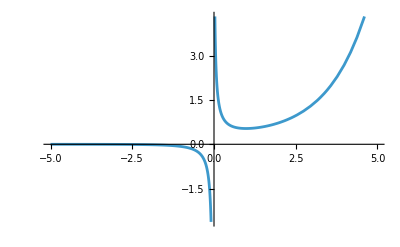

```mathematica
Plot[f[x],{x,-5,5}]
```

h. Določite zalogo vrednosti funkcije .

```mathematica
Limit[f[x],x->∞]
Limit[f[x],x->-∞]
```

∞

0

i. Izračunajte nedoločeni integral funkcije .

```mathematica
Integrate[f[x],x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
V=Pi*Integrate[f[x]^2,{x,0.5,2}]
N[V,3]  
RevolutionPlot3D[f[x],{x,0.5,2},RevolutionAxis->X]
```

1.66479

1.66479

-Graphics3D-

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll["Global`*"]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
g[x_]:=(1+x^2.1)/(3+x)
values=Table[g[x],{x,1,100}]
```

{0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883}

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
Select[values,PrimeQ[Mod[#,10]]&]
```

{}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
anonFunc=#^2+1&
```

#1^2+1&

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
newValues=anonFunc/@values
```

{1.25,2.11813,4.38873,8.66433,15.4072,24.9712,37.6338,53.6195,73.1144,96.2764,123.243,154.134,189.057,228.11,271.382,318.954,370.902,427.296,488.203,553.686,623.802,698.608,778.158,862.502,951.689,1045.77,1144.78,1248.77,1357.78,1471.85,1591.02,1715.33,1844.81,1979.5,2119.44,2264.65,2415.18,2571.05,2732.29,2898.95,3071.03,3248.59,3431.63,3620.2,3814.32,4014.01,4219.31,4430.24,4646.82,4869.07,5097.04,5330.73,5570.17,5815.39,6066.4,6323.24,6585.92,6854.46,7128.89,7409.23,7695.49,7987.71,8285.9,8590.07,8900.26,9216.47,9538.73,9867.06,10201.5,10542.,10888.6,11241.4,11600.4,11965.5,12336.8,12714.4,13098.1,13488.1,13884.4,14287.,14695.8,15111.,15532.5,15960.3,16394.5,16835.1,17282.,17735.4,18195.2,18661.4,19134.1,19613.2,20098.9,20591.,21089.6,21594.8,22106.5,22624.7,23149.5,23680.9}

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

1+2 x+x^2

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

```mathematica
rules={x->y+1}
(x^2 + 2x + 1)/. rules
```

{x→1+y}

1+2 (1+y)+(1+y)^2

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

```mathematica
(x^2 + 2x + 1)/. x->2
```

9

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

```mathematica
f[x_]:=x^5-4 x^3+x^2+3 x-2
rule2={x^n_:>2 n x^(n-1)}
f[x]/. rule2
```

{x^n_:>2 n x^(n-1)}

-2+7 x-24 x^2+10 x^4

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_]:=x^2025
g[x]/. rule2
```

4050 x^2024

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
fibRule={Fib[n_]:>Fib[n-1]+Fib[n-2]}
Nest[ReplaceAll[Fib[10],fibRule]&,Fib[10],10]
```

{Fib[n_]:>Fib[n-1]+Fib[n-2]}

Fib[8]+Fib[9]